```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
HamiltonianMin[J_,P_,FlavourSym_,γMax_,Λ_,S_,m1_,m2_,m3_,excited_,temperature_,wLeft_,wRight_,tolerance_,whichHamiltonian_:1,optimise_:True,omega_:1]:=Module[{},
ClearAll[case,proj,vCoulomb,vLinear,qhoSpect,kineticRho,kineticLam,wMin,hamiltonian,ham,sM,t1,t2,states,sM];
(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
Print["Time taken to compute t1: ", ToString[t1time]];
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
Print["Time taken to compute t2: ", ToString[t2time]];

(* Obtain projector matrix *)
proj=projector[states,FlavourSym,case];
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
(* Required matrices for hamiltonian *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];

(* Choose which Hamiltonian to use (simple temp dependence = 1, Debye screened potential = 2) *)
If[whichHamiltonian==1,
(* Hamiltonian matrix *)
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj],
ham[ω_]:=Hb2[ω,temperature,m1,m2,m3]
];

If[optimise,
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,wLeft,wRight,tolerance]];
(*Print["Time taken to find minimum: ", ToString[minTime],"s"];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin],
hamiltonian=ham[omega]
];
(*eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]]*)

(* Dump Saves, must only be saved if loadDumpSaves is True *)
If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];
DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
];
hamiltonian
]
```

Time taken to compute t1: 0.653745

Time taken to compute t2: 0.045024

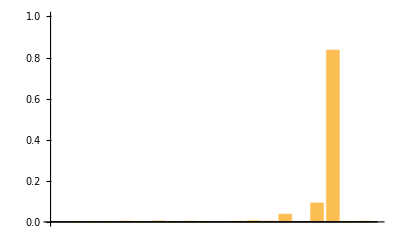

```mathematica
(* Eigenvectors of the Subscript[Λ, c] baryon excited states *)
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=0;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=6;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
excited=2;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range left *)
wRight=0.9; (* golden search range right *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

ham=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance,whichHamiltonian=1,optimise=True];
vec=Eigensystem[ham][[2,-(excited+1)]];
probs=Times[vec,vec];
BarChart[probs,PlotRange->{All,{0,1}}]
```

```mathematica
allStates[J,P,Λ,S,γMax]
```

{{0,0,0,0,0,0,1/2},{0,0,0,0,0,1,1/2},{0,0,1,0,0,0,1/2},{0,0,1,0,0,1,1/2},{0,1,0,1,0,0,1/2},{0,1,0,1,0,1,1/2},{1,0,0,0,0,0,1/2},{1,0,0,0,0,1,1/2},{0,0,2,0,0,0,1/2},{0,0,2,0,0,1,1/2},{0,1,1,1,0,0,1/2},{0,1,1,1,0,1,1/2},{0,2,0,2,0,0,1/2},{0,2,0,2,0,1,1/2},{1,0,1,0,0,0,1/2},{1,0,1,0,0,1,1/2},{1,1,0,1,0,0,1/2},{1,1,0,1,0,1,1/2},{2,0,0,0,0,0,1/2},{2,0,0,0,0,1,1/2}}

```mathematica
proj//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
√(rel[0,0,0,2]/(1/2*√(3/2))*1.)
```

1.56508

Time taken to compute t1: 0.006709

Time taken to compute t2: 0.007024

Time taken to compute t1: 0.006185

Time taken to compute t2: 0.006301

Time taken to compute t1: 0.006181

Time taken to compute t2: 0.0064

Time taken to compute t1: 0.006073

Time taken to compute t2: 0.006807

Time taken to compute t1: 0.006344

Time taken to compute t2: 0.006182

Time taken to compute t1: 0.006554

Time taken to compute t2: 0.011308

Time taken to compute t1: 0.006789

Time taken to compute t2: 0.006223

Time taken to compute t1: 0.006328

Time taken to compute t2: 0.007133

Time taken to compute t1: 0.006263

Time taken to compute t2: 0.007154

Time taken to compute t1: 0.006249

Time taken to compute t2: 0.006223

Time taken to compute t1: 0.006559

Time taken to compute t2: 0.006256

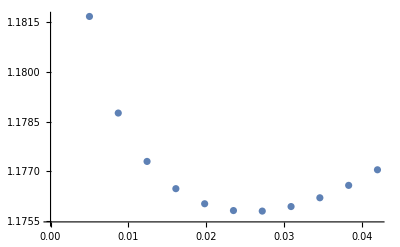

```mathematica
(* H1 TESTING *)
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=4;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=1; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

plots={};
temps={1};
For[tempStep=1,tempStep≤Length[temps],tempStep++,
temp=temps[[tempStep]];
eVals={};
start=0.005;
end=0.042;
stepSize=(end-start)/10;
omegas=Table[w,{w,start,end,stepSize}];
For[step=1,step≤Length[omegas],step++,
omega=omegas[[step]];
ham=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temp,wLeft,wRight,tolerance,whichHamiltonian=1,optimise=False,omega=omega];
eVal=Eigenvalues[ham][[-1]];
AppendTo[eVals,{omega,eVal}];
];
AppendTo[plots,eVals]
]
ListPlot[plots]

(*temperaturePlots=ListPlot[plots,
Joined->True,
PlotMarkers->Automatic,
PlotRange->{Automatic,{1.17,1.22}},
ScalingFunctions->{"Log",Automatic},
PlotLegends->{"T/T_C=0.9","T/T_C=0.99","T/T_C=0.999","T/T_C=0.9999","T/T_C=1"},
PlotTheme->"Scientific",
PlotLabel->"Λ_c(udc)",
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Arial",FontSize->14}
]*)
(*Export["plots/ch9_v1_udc_Jhalf_findingT.pdf",temperaturePlots,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]*)
```

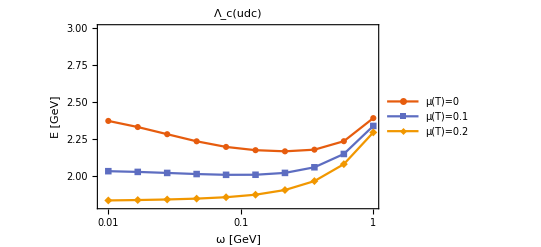

```mathematica
(* H2 TESTING *)
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=4;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0.1; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

plots={};
(*temps={0.00001,0.1,0.2,0.3,0.35,0.4};*)
temps={0.2,0.3,0.4};
For[tempStep=1,tempStep≤Length[temps],tempStep++,
temp=temps[[tempStep]];
eVals={};
(*omegas={0.0001,0.00025,0.0005,0.001,0.0025,0.005,0.01,0.025,0.05,0.1,0.25,0.5,1,2};*)
nSteps=10;
omegas=Table[0.01*((1/0.01)^(1/(nSteps-1)))^i,{i,0,nSteps-1}];
For[step=1,step≤Length[omegas],step++,
omega=omegas[[step]];
ham=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temp,wLeft,wRight,tolerance,whichHamiltonian=2,optimise=False,omega=omega];
eVal=Eigenvalues[ham][[-1]];
AppendTo[eVals,{omega,eVal}];
];
AppendTo[plots,eVals]
]
temperaturePlots=ListPlot[plots,
Joined->True,
PlotMarkers->Automatic,
PlotRange->{Automatic,{1.8,3}},
ScalingFunctions->{"Log",Automatic},
PlotLegends->{"μ(T)=0","μ(T)=0.1","μ(T)=0.2","μ(T)=0.3","μ(T)=0.35"},
PlotTheme->"Scientific",
PlotLabel->"Λ_c(udc)",
FrameLabel->{"ω [GeV]","E [GeV]"},
LabelStyle->{FontFamily->"Arial",FontSize->14}
]
(*Export["plots/ch9_v2_uuc_Jhalf_findingT.pdf",temperaturePlots,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]*)
```

```mathematica
nSteps=20;
Table[0.01*((1/0.01)^(1/(nSteps-1)))^i,{i,0,nSteps-1}]
```

{0.01,0.0127427,0.0162378,0.0206914,0.0263665,0.0335982,0.0428133,0.0545559,0.0695193,0.0885867,0.112884,0.143845,0.183298,0.233572,0.297635,0.379269,0.483293,0.615848,0.78476,1.}

```mathematica
k=(1/0.01)^(1/9)
```

1.6681

```mathematica
e[μ_]:=m1+m2+m3+(3*coeffLinear)/(2*μ)-3/2*Cqqq-(2.02*10^-3)/(m1*m2*m3)-Eigenvalues[ham[0.01,μ]][[-1]]
```

```mathematica
e[0.4]
```

-0.00550623

```mathematica
m1+m2+m3+(3*coeffLinear)/(2*0.6)-(2.02*10^-3)/(m1*m2*m3)-3/2*Cqqq
```

1.62001

```mathematica
Eigenvalues[ham[0.001,0.6]][[-1]]
```

1.62076

```mathematica
(* Finding Subscript[μ, C] *)
ClearAll[case,proj,vCoulomb,vLinear,qhoSpect,kineticRho,kineticLam,wMin,hamiltonian,ham,sM,t1,t2,states,sM];
(**** !!!TUNABLE PARAMETERS!!! ****)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=4;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0.4; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)

(* Obtain projector matrix *)
proj=projector[states,FlavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];

(* Choose which Hamiltonian to use (simple temp dependence = 1, Debye screened potential = 2) *)
(* Hamiltonian matrix *)
ham[ω_]:=Hb2[ω,temperature,m1,m2,m3,proj];
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,wLeft,wRight,tolerance]];
(*Print["Time taken to find minimum: ", ToString[minTime],"s"];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin]
```

{{1.82768,7.17037×10^-8,-0.0000119524,6.2367×10^-6,-5.24204×10^-8,-0.0000132224,0.000321096,-2.61542×10^-7,-0.0000115013,-0.0000119952},{7.17037×10^-8,1.82768,2.11261×10^-7,-8.54209×10^-8,-0.000017404,3.78924×10^-7,6.11047×10^-7,0.000230151,7.34098×10^-7,8.93999×10^-7},{-0.0000119524,2.11261×10^-7,1.82768,-8.76373×10^-6,3.85466×10^-7,-0.000013514,0.000173398,5.65489×10^-7,0.000166834,-0.0000172763},{6.2367×10^-6,-8.54209×10^-8,-8.76373×10^-6,1.82766,6.1915×10^-7,4.83992×10^-6,6.45208×10^-6,1.69111×10^-6,7.43932×10^-9,-0.0000154524},{-5.24204×10^-8,-0.000017404,3.85466×10^-7,6.1915×10^-7,1.82768,2.84097×10^-7,4.83626×10^-7,0.000219695,7.36025×10^-7,1.20076×10^-6},{-0.0000132224,3.78924×10^-7,-0.000013514,4.83992×10^-6,2.84097×10^-7,1.82768,-0.0000154478,3.94183×10^-9,0.000324171,-0.0000127096},{0.000321096,6.11047×10^-7,0.000173398,6.45208×10^-6,4.83626×10^-7,-0.0000154478,1.82737,7.20988×10^-8,-0.0000172763,0.000166825},{-2.61542×10^-7,0.000230151,5.65489×10^-7,1.69111×10^-6,0.000219695,3.94183×10^-9,7.20988×10^-8,1.82736,4.6813×10^-7,1.32523×10^-6},{-0.0000115013,7.34098×10^-7,0.000166834,7.43932×10^-9,7.36025×10^-7,0.000324171,-0.0000172763,4.6813×10^-7,1.82737,0.000166184},{-0.0000119952,8.93999×10^-7,-0.0000172763,-0.0000154524,1.20076×10^-6,-0.0000127096,0.000166825,1.32523×10^-6,0.000166184,1.82706}}

```mathematica
Eigenvalues[hamiltonian][[-1]]
```

1.82686

```mathematica
wMin
```

0.000303874

```mathematica
(* WAVEFUNCTION AT ORIGIN *)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
m1=cq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)

hamMin=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance];
eSys=Eigensystem[hamMin];
eVec=eSys[[2,-1]];
eVal=eSys[[1,-1]];
Print[eVal]
deltaMatrix3=delta3RhoMatrix[sM];
deltaMatrix1=Transpose[t1].deltaMatrix3.t1;
α[m1,m2,wMin]^3*eVec.(Transpose[proj].deltaMatrix3.proj).eVec*5.068^3*14.8/1.07176
α[m1,m2,wMin]^3*eVec.(Transpose[proj].deltaMatrix1.proj).eVec*5.068^3*14.8/1.07176
```

2.46535

26.2942

53.2018

Time taken to compute t1: 0.02807

Time taken to compute t2: 0.028175

t=0, ω=0.55688, E=14.404

{0.248452,0.248452,0.248452}

Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): {0.248452,0.248452,0.248452}

Expectation Values as ratios: {1.,1.,1.}

{0.0205762}

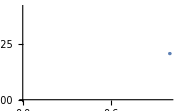

```mathematica
(* MEAN-SQUARED RADIUS *)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=3/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
FlavourSym=1;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=3/2;(* Total spin *)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
excited=0;(* Choose excited state, 0 for ground state *)
temperature=0; (* Temperature *)
wLeft=0.0001; (* golden search range start *)
wRight=0.9; (* golden search range end *)
tolerance=0.0005;(* golden search tolerance *)
(**** !!! END OF TUNABLE PARAMETERS!!! ****)


expValsData={};

hamMin=HamiltonianMin[J,P,FlavourSym,γMax,Λ,S,m1,m2,m3,excited,temperature,wLeft,wRight,tolerance];

system=Eigensystem[hamMin];

eval=system[[1,-1-excited]];
evec=system[[2,-1-excited]];

Print["t=",temperature,", ω=",wMin,", E=",eval];

(* Find expectation values of <ρ^2> *)
rhoSqrd12=1/α[m1,m2,wMin]^2 kineticRho;
rhoSqrd23=1/α1[m1,m2,m3,wMin]^2 Transpose[t1].kineticRho.t1;
rhoSqrd31=1/α2[m1,m2,m3,wMin]^2 Transpose[t2].kineticRho.t2;

rhos={rhoSqrd12,rhoSqrd23,rhoSqrd31};
expValsRho=Table[√(evec.(Transpose[proj].rhos[[i]].proj).evec)/5.068,{i,1,3}]
Print["Expectation Values of √(<SuperscriptBox[SubscriptBox[ρ, i], 2]>) for pairs {12, 23, 31} in (fm): ",expValsRho]
Print["Expectation Values as ratios: ",expValsRho/Max[expValsRho]]

(* Find expectation values of <λ^2> *)
lamSqrd12=1/β[m1,m2,m3,wMin]^2 kineticLam;
lamSqrd23=1/β1[m1,m2,m3,wMin]^2 Transpose[t1].kineticLam.t1;
lamSqrd31=1/β2[m1,m2,m3,wMin]^2 Transpose[t2].kineticLam.t2;
lams={lamSqrd12,lamSqrd23,lamSqrd31};
expValsLam=Table[evec.(Transpose[proj].lams[[i]].proj).evec,{i,1,3}];

(* Mean mass-square radius using exact method *)
expVals=expValsLam/5.068^2;
λ3Squared=expVals[[1]];
λ1Squared=expVals[[2]];
λ2Squared=expVals[[3]];
M=m1+m2+m3;
term1=(m1(m2+m3)^2)/M^3 λ1Squared;
term2=(m2(m1+m3)^2)/M^3 λ2Squared;
term3=(m3(m1+m2)^2)/M^3 λ3Squared;
RmSquared=term1+term2+term3;

AppendTo[expValsData,RmSquared]

ListPlot[expValsData]
```

```mathematica
RmSquared
```

0.0690365

```mathematica
test={{1,2,0,0,0,0},{3,4,0,0,0,0},{0,0,9,10,0,0},{0,0,11,12,0,0},{0,0,0,0,5,6},{0,0,0,0,7,8}};
test//MatrixForm
```

(1 | 2 | 0 | 0 | 0 | 0
3 | 4 | 0 | 0 | 0 | 0
0 | 0 | 9 | 10 | 0 | 0
0 | 0 | 11 | 12 | 0 | 0
0 | 0 | 0 | 0 | 5 | 6
0 | 0 | 0 | 0 | 7 | 8)

```mathematica
Eigenvalues[test]*1.
```

{21.0948,13.1521,5.37228,-0.372281,-0.152067,-0.0948101}

```mathematica
Eigenvalues[{{1,2},{3,4}}]*1.
```

{5.37228,-0.372281}